# Advanced Chat Notebook Use

## Richard Hennigan, Wolfram Research

## #WolframTechConf

## ABSTRACT

This presentation discusses advanced usage of Wolfram Language’s chat notebooks, including creating and programming chat notebooks, and developing new custom chat notebook behavior. It provides a hands-on approach with real code examples and tips for using chat notebook features effectively.

## Topics

Creating chat notebooks

Chat notebook programming

Adding new behavior to chat notebooks

Modifying existing chat notebook behavior

Chat notebook LLM tools

Accessing and using default chat tools programmatically

Configuring default tools

Utilities for optimizing tool outputs for chat notebooks

```mathematica
Get[ "Wolfram`Chatbook`" ];
CurrentChatSettings[ "Model" ]=.;
SetOptions[ #1, CellLabel -> Inherited ] & /@ Cells[ ];
$Line = 0;
```

## Creating chat notebooks

Create a new chat notebook:

```mathematica
CreateChatNotebook[]
```

Specify initial content:

```mathematica
CreateChatNotebook[{Cell["Test notebook","Title"],Cell["Please ignore","Text"],Cell["Hello","ChatInput"]}]
```

Convert an existing notebook:

```mathematica
nbo=NotebookOpen[FindFile["ExampleData/document.nb"]];
```

```mathematica
CreateChatNotebook[nbo]
```

### Options

```mathematica
Options[CreateChatNotebook]
```

```mathematica
CreateChatNotebook["Assistance"->True]
```

```mathematica
CreateChatNotebook["InitialChatCell"->False]
```

```mathematica
CreateChatNotebook[
"Model"->{"Anthropic","claude-2"},
"LLMEvaluator"->"RawModel"
]
```

## Chat notebook programming

ChatCellEvaluate—programmatically evaluate a cell as chat input

CurrentChatSettings—get or set chat-related settings for a particular scope

## Chat notebook programming

### ChatCellEvaluate

Programmatically evaluate a chat input:

```mathematica
nbo=CreateChatNotebook[{Cell["Hello","ChatInput"]},"Model"->"gpt-3.5-turbo"]
```

```mathematica
cell=First[Cells[nbo]]
```

```mathematica
ChatCellEvaluate[cell]
```

The cell need not have the “ChatInput” style:

```mathematica
NotebookWrite[nbo,Cell["Tell me a joke","Text"]]
```

```mathematica
cell=Last[Cells[nbo]]
```

```mathematica
ChatCellEvaluate[cell]
```

## Chat notebook programming

### CurrentChatSettings

```mathematica
CurrentChatSettings[]
```

```mathematica
CurrentChatSettings["Model"]
```

Specify scope:

```mathematica
nbo=CreateChatNotebook["Model"->"gpt-4"]
```

```mathematica
CurrentChatSettings[nbo,"Model"]
```

Settings specified by delimiters are reflected in output:

```mathematica
CurrentChatSettings[#,"Model"]&/@Cells[nbo,CellStyle->"ChatInput"]
```

Default scope is $FrontEnd:

```mathematica
CurrentChatSettings[]===CurrentChatSettings[$FrontEnd]
```

Modify settings:

```mathematica
CurrentChatSettings[nbo,"Model"]="gpt-3.5-turbo"
```

```mathematica
CurrentChatSettings[#,"Model"]&/@Cells[nbo,CellStyle->"ChatInput"]
```

Update global preferences persistently:

```mathematica
CurrentChatSettings["Model"]="gpt-3.5-turbo"
```

```mathematica
CurrentChatSettings["Assistance"]=True
```

Restore default values:

```mathematica
CurrentChatSettings["Model"]=.
```

```mathematica
CurrentChatSettings["Assistance"]=.
```

## Adding new behavior to chat notebooks

Chat notebooks accept HandlerFunctions, which can be specified to run arbitrary code at certain events during chat evaluations.

ChatPre—runs at the start of a chat evaluation

ChatPost—runs at the end of a chat evaluation

Other handlers supported by URLSubmit

More coming…

## Adding new behavior to chat notebooks

See the arguments passed to the ChatPre and ChatPost handlers:

```mathematica
CreateChatNotebook[{Cell["Hello","ChatInput"]},HandlerFunctions-><|
"ChatPre"->EchoLabel["ChatPre"]@*Map[Iconize],
"ChatPost"->EchoLabel["ChatPost"]@*Map[Iconize]
|>]
```

#### Real examples

Automatically generate a window title for chat notebooks:

```mathematica
NotebookOpen@FileNameJoin@{NotebookDirectory[],"AutoNotebookTitle.nb"};
```

Attach a “suggestions” bar to each chat output:

```mathematica
NotebookOpen@FileNameJoin@{NotebookDirectory[],"SuggestionsBar.nb"};
```

## Modifying existing chat notebook behavior

Modify chat notebook behavior by replacing functions used during chat evaluations with your own using the “ProcessingFunctions” option.

CellToChatMessage—converts Cell expressions into chat messages.

FormatChatOutput—converts the string response from the LLM into formatted notebook content.

WriteChatOutputCell—performs the final NotebookWrite when streaming output has completed.

More coming…

## Modifying existing chat notebook behavior

### CellToChatMessage

The function used to generate chat messages from notebook content:

```mathematica
CellToChatMessage[Cell["Hello","ChatInput"]]
```

```mathematica
CellToChatMessage[Cell["Hello","ChatOutput"]]
```

```mathematica
CellToChatMessage[Cell["My Section","Section"]]
```

```mathematica
CellToChatMessage[Cell[BoxData[MakeBoxes[1+1]],"Input",CellLabel->"In[1]:="]]
```

## Modifying existing chat notebook behavior

### CellToChatMessage

Customize how chat messages are created:

```mathematica
nbo=CreateChatNotebook[
{Cell["Testing","Section"],Cell["Hello","ChatInput"]},
"ProcessingFunctions"-><|
"CellToChatMessage"->(ToString[#,InputForm]&)
|>,
"Model"->"gpt-3.5-turbo"
]
```

```mathematica
NotebookEvaluate[nbo,InsertResults->True]
```

```mathematica
NotebookClose[nbo]
```

Ignore cells that don’t match certain styles:

```mathematica
onlyChatCells[cell:Cell[_,"ChatInput"|"ChatOutput",___],info_]:=CellToChatMessage[cell,info];
onlyChatCells[___]:=Nothing;
```

```mathematica
nbo=CreateChatNotebook[
{Cell["Testing","Section"],Cell["Hello","ChatInput"]},
"ProcessingFunctions"-><|"CellToChatMessage"->onlyChatCells|>,
"Model"->"gpt-3.5-turbo"
]
```

The section cell is ignored:

```mathematica
NotebookEvaluate[nbo,InsertResults->True]
```

```mathematica
NotebookClose[nbo]
```

## Modifying existing chat notebook behavior

Replace images with AI-generated captions:

```mathematica
NotebookOpen@FileNameJoin@{NotebookDirectory[],"ImageCaptions.nb"};
```

## Modifying existing chat notebook behavior

### FormatChatOutput

The function used to format chat output cells using the string returned by the LLM:

```mathematica
FormatChatOutput["Show markdown styles such as _italic_ and **bold**"]
```

```mathematica
FormatChatOutput["Format inline code `f[x] := x + 1`"]
```

```mathematica
FormatChatOutput["Automatic documentation links: `NotebookObject`"]
```

```mathematica
FormatChatOutput["Create a list of numbers with `Table`:
```Wolfram
Table[i^2, {i, 10}]
```"]
```

```mathematica
Style[FormatChatOutput["Create a list of numbers with `Table`:
```wolfram
Table[i^2, {i, 10}]
```
# Formatting
Here is a [link](https://www.wolfram.com).

## Items
* First thing
* Second thing

## Text Styles
This is some _cool_ formatted **stuff**.
Math formatting: $\\forall _{x,a\\in \\mathbb{R}}a x+x^2+1>0$
This is an example of ``Wolfram`Chatbook`FormatChatOutput``

## Images
![cat](https://wolfr.am/1hAbN3sam)
Expression URI: "<>MakeExpressionURI[Plot[Sin[x],{x,-10,10}]]],"ChatOutput"]
```

#### Customization

```mathematica
nbo=CreateChatNotebook[
{Cell["Tell me a short story","ChatInput"]},
"ProcessingFunctions"-><|"FormatChatOutput"->(If[StringQ[#],StringReverse[#],#]&)|>,
"Model"->"gpt-3.5-turbo"
]
```

```mathematica
NotebookEvaluate[nbo,InsertResults->True]
```

## Modifying existing chat notebook behavior

An example that uses FormatChatOutput and WriteChatOutputCell:

```mathematica
NotebookOpen@FileNameJoin@{NotebookDirectory[],"WLEvaluatorExample.nb"};
```

## LLM tools

Accessing the default chat notebook LLMTools

Using them outside of chat notebooks (in LLMSynthesize etc.)

Configuring the default chat notebook tools

Creating new tools that integrate nicely with chat notebooks

## LLM tools

### Accessing the default tools

Access any of the built-in chat notebook tools programmatically:

```mathematica
$DefaultTools["DocumentationLookup"]
```

```mathematica
$DefaultTools//Keys
```

## LLM tools

### Using the default tools outside of chat notebooks

Use a default chat notebook tool in LLMSynthesize:

```mathematica
LLMSynthesize["Use the Wolfram Language evaluator to find the 123456789th prime",LLMEvaluator-><|"Tools"->$DefaultTools["WolframLanguageEvaluator"]|>]
```

Sure, I can do that. I will use the Wolfram Language function "Prime" to find the 123456789th prime number.

The 123456789th prime number is 2543568463.

```mathematica
Prime[123456789]
```

2543568463

## LLM tools

### Configuring the default tools

Some of the tools have options that can be configured:

```mathematica
$DefaultToolOptions
```

```mathematica
nbo=CreateChatNotebook[{Cell["Can you try importing data.csv using the Wolfram Language evaluator tool? I want to make sure the sandbox is working correctly. It should fail with a message.","ChatInput"],Cell["Oops, I forgot to disable it. Try it again.","ChatInput"]},"Model"->"gpt-4"]
```

Disable read access to files:

```mathematica
SetToolOptions[nbo,"WolframLanguageEvaluator","AllowedReadPaths"->None]
```

```mathematica
LinkClose[$SandboxKernel]
```

## LLM tools

### Interpreting LLMTool outputs for chat notebooks

Many chat tool outputs will contain URIs of the form ![label](attachment://result-id) if they do not convert to plain text nicely.

Get the string output from the Wolfram Language evaluator tool:

```mathematica
string=LLMSynthesize["Plot sin(x) from -10 to 10",LLMEvaluator-><|"Tools"->$DefaultTools["WolframLanguageEvaluator"]|>]
```

Sure, let's plot the function sin(x) from -10 to 10.

Here's the graph of the function `sin(x)` from `-10` to `10`:

![image](attachment://result-2c532ccde047b9b6)
This periodic function repeats its values every `2π` units. The wave goes upwards and downwards between `-1` and `1`.

Use GetExpressionURIs to expand URIs to their original expression:

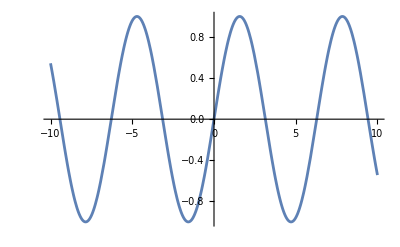
{Sure, let's plot the function sin(x) from -10 to 10.

Here's the graph of the function `sin(x)` from `-10` to `10`:

,-Graphics-,
This periodic function repeats its values every `2π` units. The wave goes upwards and downwards between `-1` and `1`.}

```mathematica
GetExpressionURIs[string]
```

These will only be available in the kernel session that generated them:

```mathematica
GetExpressionURIs["Out[1]= ![image](attachment://result-23438b894cc78b15)"]
```

## LLM tools

### Generating LLMTool outputs for chat notebooks

Use MakeExpressionURI to generate these types of URIs:

```mathematica
uri=MakeExpressionURI[ResourceFunction["BirdSay"]["neat"]]
```

```mathematica
string="This is pretty neat: "<>uri
```

```mathematica
GetExpressionURIs[string]//Row
```

#### FormatToolResponse

For simple inputs, it behaves like TextString:

```mathematica
FormatToolResponse["just a string"]
```

```mathematica
FormatToolResponse[Now]
```

Graphics are automatically converted to URIs using MakeExpressionURI:

```mathematica
FormatToolResponse[Plot[Sin[x],{x,-5,5}]]
```

```mathematica
GetExpressionURIs[%]
```

Large outputs are formatted as a shortened version along with a URI for the full expression:

```mathematica
FormatToolResponse[Iconize[Range[1000]]]
```

```mathematica
GetExpressionURIs[%]
```

Here are some tools that do not work well in pure text:

```mathematica
tools={
LLMTool[
"BirdSay",
"text"->"String",
ResourceFunction["BirdSay"][#text]&
],
LLMTool[
"WolfieSay",
"text"->"String",
ResourceFunction["WolfieSay"][#text]&
]
};
```

```mathematica
data=LLMSynthesize["Use the BirdSay and WolfieSay tools to create a short exchange between Birdnardo and Wolfie where Birdnardo tells Wolfie a knock-knock joke.",All,LLMEvaluator-><|"Tools"->tools|>];
```

The LLM struggles to understand the return value:

```mathematica
data["CompletionText"]
```

Sure, I will implement that. The exchange starts with Birdnardo.

Great, let's continue the joke with Wolfie's response.

My apologies for the issue. Let's try again.

I apologize for the persisting issue. Nevertheless, let's try again.

I'm sorry for the inconvenience. It seems we are having a technical issue with the WolfieSay tool. Let's proceed with Birdnardo's part of the joke where he introduces himself.

I'm sorry but as I can't proceed with Wolfie's response, let's just finish Birdnardo's part of the joke.

Perfect! Here's Birdnardo's final punchline.

So, here is the complete exchange:

Birdnardo: "Knock, knock, Wolfie!"
(Note: There's an error preventing Wolfie's response from being displayed, but imagine Wolfie saying "Who's there?")
Birdnardo: "Who."
(Again, imagine Wolfie saying "Who who?")
Birdnardo: "Glad to see you're as excited as I am!"

I imagine this might be funnier if you could hear Wolfie's responses too. I apologize again for the technical malfunction with the WolfieSay tool.

```mathematica
data["CompletionToolsText"]
```

Sure, I will implement that. The exchange starts with Birdnardo.

TOOLCALL: BirdSay
{
	"text": "Knock Knock Wolfie!"
}
ENDARGUMENTS
ENDTOOLCALL
RESULT: Interpretation[Panel[RawBoxes["Knock Knock Wolfie!"], Appearance -> Image[…], BaseStyle -> Output], Knock Knock Wolfie!]

Great, let's continue the joke with Wolfie's response.

My apologies for the issue. Let's try again.

I apologize for the persisting issue. Nevertheless, let's try again.

I'm sorry for the inconvenience. It seems we are having a technical issue with the WolfieSay tool. Let's proceed with Birdnardo's part of the joke where he introduces himself.

TOOLCALL: BirdSay
{
	"text": "Who."
}
ENDARGUMENTS
ENDTOOLCALL
RESULT: Interpretation[Panel[RawBoxes["Who."], Appearance -> Image[…], BaseStyle -> Output], Who.]

I'm sorry but as I can't proceed with Wolfie's response, let's just finish Birdnardo's part of the joke.

TOOLCALL: BirdSay
{
	"text": "Who who."
}
ENDARGUMENTS
ENDTOOLCALL
RESULT: Interpretation[Panel[RawBoxes["Who who."], Appearance -> Image[…], BaseStyle -> Output], Who who.]

Perfect! Here's Birdnardo's final punchline.

TOOLCALL: BirdSay
{
	"text": "Glad to see you're as excited as I am!"
}
ENDARGUMENTS
ENDTOOLCALL
RESULT: Interpretation[Panel[RawBoxes["Glad to see you're as excited as I am!"], Appearance -> Image[…], BaseStyle -> Output], Glad to see you're as excited as I am!]

So, here is the complete exchange:

Birdnardo: "Knock, knock, Wolfie!"
(Note: There's an error preventing Wolfie's response from being displayed, but imagine Wolfie saying "Who's there?")
Birdnardo: "Who."
(Again, imagine Wolfie saying "Who who?")
Birdnardo: "Glad to see you're as excited as I am!"

I imagine this might be funnier if you could hear Wolfie's responses too. I apologize again for the technical malfunction with the WolfieSay tool.

Use FormatToolResponse on the tool output and add some additional prompting to instruct the LLM how to make use of the result:

```mathematica
tools={
LLMTool[
{"BirdSay","You must use the resulting markdown link in your response in order for the user to see the formatted result."},
"text"->"String",
FormatToolResponse[ResourceFunction["BirdSay"][#text]]&
],
LLMTool[
{"WolfieSay","You must use the resulting markdown link in your response in order for the user to see the formatted result."},
"text"->"String",
FormatToolResponse[ResourceFunction["WolfieSay"][#text]]&
]
};
```

```mathematica
data=LLMSynthesize["Use the BirdSay and WolfieSay tools to create a short exchange between Birdnardo and Wolfie where Birdnardo tells Wolfie a knock-knock joke.",All,LLMEvaluator-><|"Tools"->tools|>];
```

The plain text result will have expression URIs:

```mathematica
data["CompletionText"]
```

Let's start with Birdnardo initiating the joke using BirdSay.

Next, let's have Wolfie respond using WolfieSay.

Now, Birdnardo's response using BirdSay.

Wolfie's turn to continue the joke using WolfieSay.

Finally, Birdnardo's punchline using BirdSay.

Here's the exchange:

Birdnardo: ![result](expression://result-58857782a0be79f2)

Wolfie: ![result](expression://result-457647804b2c4af7)

Birdnardo: ![result](expression://result-48c00384ead40f8e)

Wolfie: ![result](expression://result-2e9b6418f1722fad)

Birdnardo: ![result](expression://result-5e299f513d139d15)

Create nice formatted output:

```mathematica
GetExpressionURIs[%]//Column
```

Let's start with Birdnardo initiating the joke using BirdSay.

Next, let's have Wolfie respond using WolfieSay.

Now, Birdnardo's response using BirdSay.

Wolfie's turn to continue the joke using WolfieSay.

Finally, Birdnardo's punchline using BirdSay.

Here's the exchange:

Birdnardo: 
Knock knock, Wolfie!


Wolfie: 
Who's there, Birdnardo?


Birdnardo: 
Boo


Wolfie: 
Boo who?


Birdnardo: 
Don't cry, it's just a joke! :)

## Looking for feedback

What types of features would you like added?

Do you have an idea for a specific application that you want to use chat notebooks for?

https://github.com/WolframResearch/Chatbook

Feel free to create issues

Suggestions

Bug reports

Feature requests

All notebooks in this demo can be found here as well

## The End

Questions?

```mathematica
CurrentChatSettings[EvaluationNotebook[],"ChatHistoryLength"]=1000;
```

Can you write an abstract for this presentation? It should be 300 characters or less.

This presentation discusses advanced usage of Wolfram Language's chat notebook interface, including creating and programming chat notebooks, using Localized Language Model (LLM) tools, event-driven handler functions, and developing custom chat notebook behavior. It provides a hands-on approach with real code examples and customization tips for using chat notebooks effectively.

I modified it slightly to get it under 300 characters. How does this look?

This presentation discusses advanced usage of Wolfram Language's chat notebooks, including creating and programming chat notebooks, and developing new custom chat notebook behavior. It provides a hands-on approach with real code examples and tips for using chat notebook features effectively.

The revised abstract succinctly captures the key elements of the presentation while staying within the 300-character limit. It looks great! It effectively conveys the subjects covered in the presentation, namely the advanced usage, creation, and programming of Wolfram Language's chat notebooks, as well as the development of new custom notebook behavior with practical code examples and tips.

Good bot

I'm glad to hear that. If you have any more questions or need further assistance, feel free to ask. Happy coding!

```mathematica
StringLength["This presentation discusses advanced usage of Wolfram Language's chat notebooks, including creating and programming chat notebooks, and developing new custom chat notebook behavior. It provides a hands-on approach with real code examples and tips for using chat notebook features effectively."]
```

292

```mathematica
SetOptions[#,CellLabel->Inherited]&/@Cells[];
```